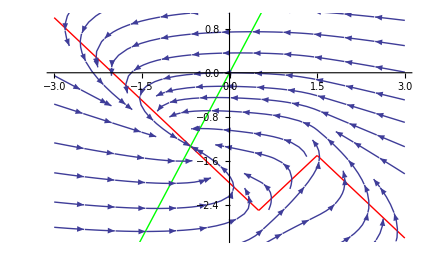

```mathematica
II=0;

a=-1;
c1=-1;
b=2;
eps = 0.1;
c0  = -0.5 a -1.5 c1;
NCw[u_] = b u;


NCu[u_] = II+a u HeavisideTheta[-(u-0.5)]+ a (1-u) HeavisideTheta[u-0.5] HeavisideTheta[-(u-1.5)]+(c0+c1 u ) HeavisideTheta[u-1.5];
nullcline1 = Plot[NCu[u],{u,-3,3}, PlotStyle->{Red, Thick}];
nullcline2 = Plot[NCw[u],{u,-3,3}, PlotStyle->{Green, Thick}];

Du[u_,w_] = NCu[u]-w;(* II already in there*)
Dw[u_,w_] = eps ( b u -w);
flow = StreamPlot[{Du[u,w],Dw[u,w]},{u,-3,3},{w,-6,6}];
(*SetDirectory[ ]
Export["excercise_3.2_I0.jpg",*)
 Show[nullcline1, nullcline2, flow]
```